## Twitter

```mathematica
tw = ServiceConnect["Twitter","connection-026ffb585d6c6afcd8c5059e8901fb26"]
```

ServiceObject[…]

## Extracción de Tweets

```mathematica
ExportTweets[users_,start_,end_,path_]:=Module[{twlist,date,todaystweets,dir},
Do[twlist=tw["TweetList", "Username"->follow,"Elements"-> "FullData",MaxItems->4000];
date=start;
While[date≠end,
	date=DatePlus[date,1];
	todaystweets = Select[twlist,DateWithinQ[date,#["Date"]]&];
dir=path<>follow;
If[Not@DirectoryQ[dir],CreateDirectory[dir]];
Export[dir<>"\\"<>DateString[date,"ISODate"]<>".csv",
	Dataset@AssociationThread[
	Normal@todaystweets[All,"ID"],
	Normal@GetHyperlinks@todaystweets]];
];
,{follow,users}]
]
```

### Usuario

```mathematica
twlist=tw["TweetList", "Username"->"AristeguiOnline","Elements"-> "FullData",MaxItems->200]
```

```mathematica
ExportTweets[users,DateObject["2020-07-11"],Yesterday,"C:\\Users\\User\\Documents\\Proyectos\\Tweets\\caracterizacion_comentocracia\\data\\"]
```

```mathematica
users={"AristeguiOnline", "Forbes_Mexico", "LaJornada","ELDEBATE","sopitas","El_Universal_Mx","Milenio","diariodejuarez","Excelsior","proceso","sdpnoticias","eldeforma","SinEmbargoMX","Planoinforma","vanguardiamx","PeriodicoZocalo","elnorte","gibranrr","Pajaropolitico"};
```

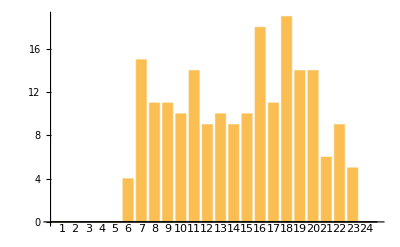

```mathematica
histdata=Normal@CountsBy[twlist[[All,"Date"]],#["Hour"]&];
BarChart[If[KeyExistsQ[histdata,#],#/.histdata,0]&/@Range@24,ChartLabels->Range@24]
```

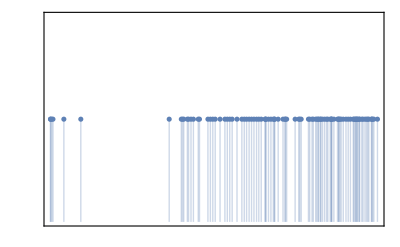

```mathematica
ttl=tw["TweetTimeline", "Username"->"Forbes_Mexico",MaxItems->100]
```

### Hyperlink

```mathematica
GetHyperlinks[data_]:=Select[#,StringMatchQ["http"~~__]]&/@TextWords/@data[All,"Text"]
```

```mathematica
wihyperlinks=GetHyperlinks[twlist⟦Range@5⟧]
```

```mathematica
tw["GetTweet","TweetID"-> twlist⟦1,"ID"⟧,"Elements"->"FullData"]
```

### Cuentas HUBs

```mathematica
HUBs=tw["UserIDSearch","Query"->"#Coronavirus",MaxItems->20];
Dataset[tw["UserData","UserID"->#]&/@HUBs]
```

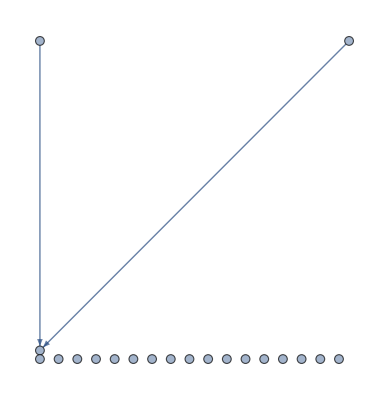

```mathematica
tw["SearchMentionNetwork","Query"->"#Coronavirus"]
```

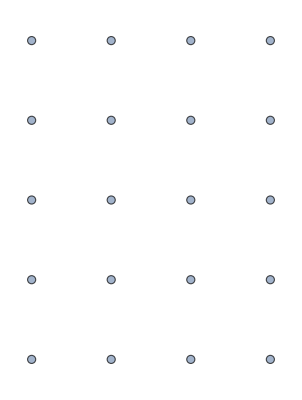

```mathematica
tw["SearchReplyToNetwork","Query"->"#Coronavirus"]
```

### Tweets HUBs

```mathematica
searchHUBs=tw["TweetSearch","Query"->"#Coronavirus",MaxItems->20,Language->Entity["Language","Spanish"],"ResultType"-> "Popular"]
```

```mathematica
keys = Keys@First@searchHUBs
```

### Localidad

```mathematica
loc=FindGeoLocation[Entity["City", {"Queretaro","Queretaro","Mexico"}]];
GeoGraphics@GeoDisk[loc,Quantity[30,"km"]]
```

-Graphics-

```mathematica
searchloc=tw["TweetSearch","Query"->"Semaforo Rojo",MaxItems->500,GeoLocation->loc,"Radius"-> Quantity[30, "Kilometers"],"ResultType"->"Recent"]
```

Dataset[<>]

```mathematica
Entity["Language","Spanish"]
```

Spanish

```mathematica
First@Normal@searchloc[All,"Text"]
```

RT @universalqro: #SemáforoRojo 🚦 Caen ventas de restaurantes en Querétaro, luego de que gobierno federal puso en semáforo rojo a la entida…

```mathematica
TextTranslation["Como esta tu perro azul",Entity["Language","Spanish"]-> Entity["Language","English"]]
```

Like this your blue dog

```mathematica
TextTranslation[First@Normal@searchloc[All,"Text"],Entity["Language","Spanish"]-> Entity["Language","English"]]
```

RT @universalqro: #SemáforoRojo 🚦 Caen sales of restaurants in Querétaro, after federal government put the ennt...

```mathematica
Keys@First@searchloc
```

```mathematica
Import[]
```

### Frecuencias

```mathematica
FilterTweets[tweets_]:=StringReplace[RemoveDiacritics@ToLowerCase@tweets,{RegularExpression["[http]*[s]*[:][\\/\\/][a-z0-9.\\/]+[ ]*"]->" ",RegularExpression["[rt: ]*[rt ]*[\\@][a-z0-9]*[:]*"]->" ",RegularExpression["[^a-z\\s:]"]|":"->" "}];
```

```mathematica
tweets=FilterTweets[#["Text"]]&/@(Normal@searchHUBs);
```

```mathematica
Stopwords=Import["https://countwordsfree.com/stopwords/spanish","Data"]⟦2,All,2⟧;
```

```mathematica
RemoveStopWords[doc_,stopWords_]:=StringDelete[doc,WordBoundary~~Alternatives@@stopWords~~WordBoundary,IgnoreCase->True];
```

```mathematica
processedTweets=Select[DeleteDuplicates[RemoveStopWords[TextWords[#],Stopwords]],Not@*StringMatchQ[""]]&/@tweets;
```

```mathematica
significantWords=Take[Reverse[SortBy[Tally[Flatten[processedTweets]],Last]],10];
quantities=N[#⟦2⟧/Length@tweets]&/@significantWords;
pieChart=PieChart[quantities,ChartLabels->Placed[significantWords⟦All,1⟧,"RadialCallout"],LabelingFunction->(PercentForm@*N@#&)]
```

-Graphics-